```mathematica
ClearAll["Global`*"]
```

```mathematica
A1<->X<->A2
```

```mathematica
v1=k1*(A1- x[t]/K1);
v2=k2*(x[t]-A2/K2);
```

```mathematica
DSolve[{x'[t]==v1-v2/.{K1->1,K2->1,A1->2,A2->1},x[0]==0},x[t],t]
```

{{x[t]→-((-1+ⅇ^((-k1-k2) t)) (2 k1+k2))/(k1+k2)}}

```mathematica
?N
```

System`N

Attributes[N]={Protected}
 
N/:Default[N,2]:={MachinePrecision,MachinePrecision}

```mathematica
S=N[(2 k1+k2)/(k1+k2)/.{k1->4*10^8,k2->1},10]
```

1.999999998

```mathematica
A1<->X1<->X2<->A2
```

```mathematica
v1=k1*(A1- x1[t]/K1);
v2=k2*(x1[t]-x2[t]/K2);
v3=k3*(x2[t]-A2/K3);
```

```mathematica
sol=Simplify[DSolve[{x1'[t]==v1-v2,x2'[t]==v2-v3,x1[0]==0,x2[0]==0}/.{K1->1,K2->1,K3->1,A1->2,A2->1},{x1[t],x2[t]},t]];
```

```mathematica
x1f[t_]=x1[t]/.sol[[1]][[1]];
x2f[t_]=x2[t]/.sol[[1]][[2]];
```

```mathematica
-1/2 (k1+2 k2+k3+√(k1^2+4 k2^2-2 k1 k3+k3^2))
√(k1^2+4 k2^2-2 k1 k3+k3^2)
√(k1^2+4 k2^2-2 k1 k3+k3^2)
1/2 (k1+2 k2+k3+√(k1^2+4 k2^2-2 k1 k3+k3^2))
```

```mathematica
Simplify[Expand[(k1+2 k2+k3)^2]-(k1^2+4 k2^2-2 k1 k3+k3^2)]
```

4 (k2 k3+k1 (k2+k3))

```mathematica
?Limit
```

Limit[expr,x→x_0] finds the limiting value of expr when x approaches x_0.

```mathematica
Simplify[Limit[x1f[t],t->Infinity]]
```

Limit[-((ⅇ^(-1/2 (k1+2 k2+k3+√(k1^2+4 k2^2-2 k1 k3+k3^2)) t) (-2 (-1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)) k1^2 (k2+k3)+k2 k3 (2 (-1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)) k2+(-1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)) k3+(1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)-2 ⅇ^(1/2 (k1+2 k2+k3+√(k1^2+4 k2^2-2 k1 k3+k3^2)) t)) √(k1^2+4 k2^2-2 k1 k3+k3^2))+k1 (4 (-1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)) k2^2+2 k3 ((-1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)) k3+(1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)-2 ⅇ^(1/2 (k1+2 k2+k3+√(k1^2+4 k2^2-2 k1 k3+k3^2)) t)) √(k1^2+4 k2^2-2 k1 k3+k3^2))+k2 (3 (-1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)) k3+2 (1+ⅇ^(√(k1^2+4 k2^2-2 k1 k3+k3^2) t)-2 ⅇ^(1/2 (k1+2 k2+k3+√(k1^2+4 k2^2-2 k1 k3+k3^2)) t)) √(k1^2+4 k2^2-2 k1 k3+k3^2)))))/(2 √(k1^2+4 k2^2-2 k1 k3+k3^2) (k2 k3+k1 (k2+k3)))),t→∞]

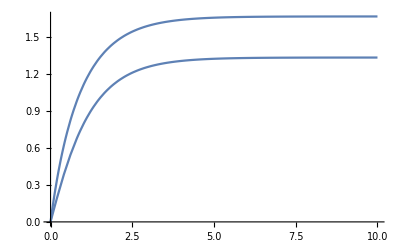

```mathematica
Plot[{x1f[t],x2f[t]}/.{k1->1,k2->1,k3->1},{t,0,10},PlotRange->All]
```

```mathematica
v1=k1*(A1- x1/K1);
v2=k2*(x1-x2/K2);
v3=k3*(x2-A2/K3);
Solve[{v1==v2,v2==v3}/.{K1->1,K2->1,K3->1},{x1,x2}]
```

{{x1→-(-A1 k1 k2-A1 k1 k3-A2 k2 k3)/(k1 k2+k1 k3+k2 k3),x2→-(-A1 k1 k2-A2 k1 k3-A2 k2 k3)/(k1 k2+k1 k3+k2 k3)}}